```mathematica
soln[k1_,k2_,ks_,kk_,g_,m_,vi_,pi_]:=Module[{f,fs,N,diff},
N = g m;

fs=ks+(F[t]/N-ks)ⅇ^(-k2 Abs[F[t]]/(ks N));
f=-Sign[y'[t]](kk+(fs-kk)ⅇ^(-k1 Abs[y'[t]]));
diff={m y''[t]==F[t]+f N,
y'[0]==vi,
y[0]==pi};

NDSolve[diff,y,{t,0,10}]];
```

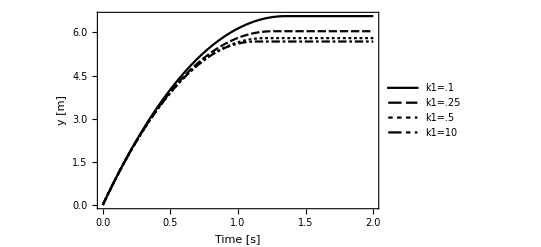

```mathematica
F[t_]=5;
k1=Plot[Evaluate[y[t]/.soln[#,10,1.4,1.0,9.8,5,10,0]&/@{.1,.25,.5,10}],
{t,0,2},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"k1=.1","k1=.25","k1=.5","k1=10"},
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'k1'"}}]
```

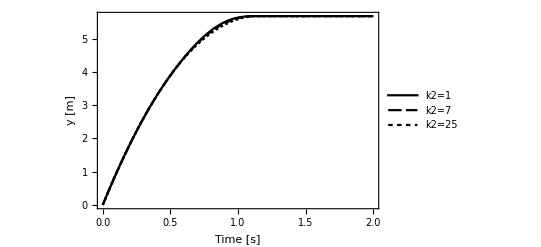

```mathematica
F[t_]=5;
k21=Plot[Evaluate[y[t]/.soln[10,#,1.4,1.0,9.8,5,10,0]&/@{1,7,25}],
{t,0,2},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"k2=1","k2=7","k2=25"},
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'k2'"}}]
```

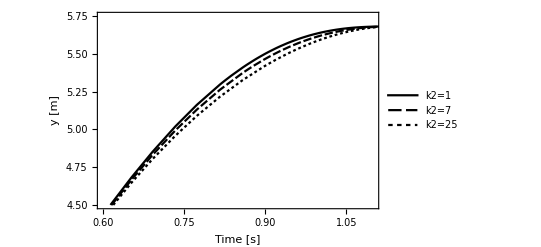

```mathematica
F[t_]=5;
k22=Plot[Evaluate[y[t]/.soln[10,#,1.4,1,9.8,5,10,0]&/@{1,7,25}],
{t,0,2},
PlotRange->{{.6,1.1},{4.5,5.75}},
PlotTheme->"Monochrome",
PlotLegends->{"k2=1","k2=7","k2=25"},
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'k2'"}}]
```

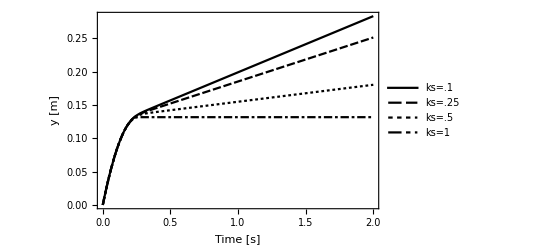

```mathematica
F[t_]=30;
ks=Plot[Evaluate[y[t]/.soln[10,10,#,1,9.8,5,1,0]&/@{.1,.25,.5,1}],
{t,0,2},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"ks=.1","ks=.25","ks=.5","ks=1"},
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'ks'"}}]
```

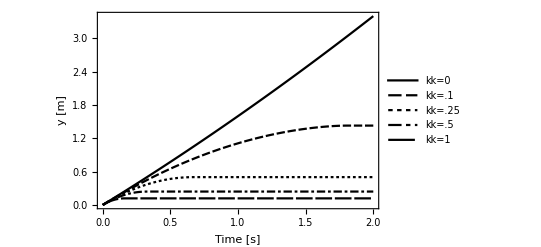

```mathematica
F[t_]=1;
kk=Plot[Evaluate[y[t]/.soln[10,10,1.4,#,9.8,5,1.5,0]&/@{0,.1,.25,.5,1}],
{t,0,2},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"kk=0","kk=.1","kk=.25","kk=.5","kk=1"},
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'kk'"}}]
```

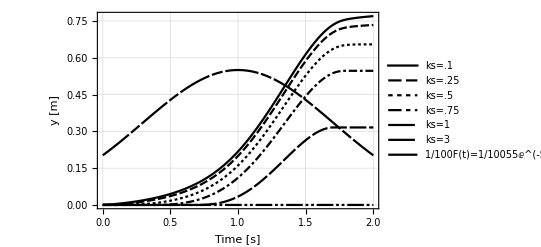

```mathematica
F[t_]=55 ⅇ^(-(t-1)^2);
ksF=Plot[Evaluate[{y[t]/.soln[10,10,#,1.0,9.8,5,0,0]&/@{.1,.25,.5,.75,1,3},1/100 F[t]}],
{t,0,2},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"ks=.1","ks=.25","ks=.5","ks=.75","ks=1","ks=3","1/100F(t)=1/10055ⅇ^(-SuperscriptBox[(t - 1), 2]) [N]"},
GridLines->Automatic,
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'ks' With Time Dependant F(t)"}}]
```

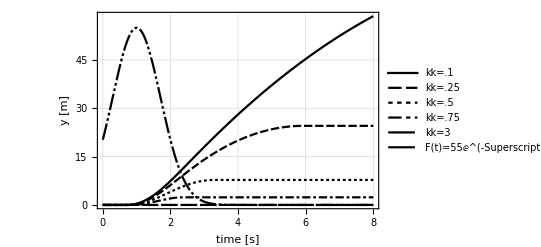

```mathematica
F[t_]=55 ⅇ^(-(t-1)^2);
kkF=Plot[Evaluate[{y[t]/.soln[10,10,1,#,9.8,5,0,0]&/@{.1,.25,.5,.75,3},F[t]}],
{t,0,8},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"kk=.1","kk=.25","kk=.5","kk=.75","kk=3","F(t)=55ⅇ^(-SuperscriptBox[(t - 1), 2]) [N]"},
GridLines->Automatic,
Frame->True,
FrameLabel->{{"y [m]",None},{"time [s]","'y' Varying 'kk' With Time Dependant F(t)"}}]
```

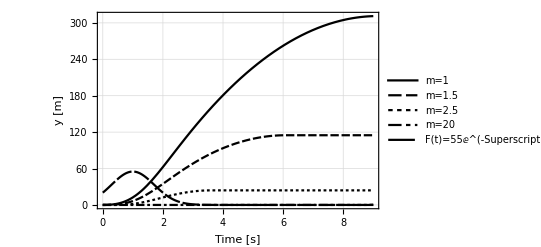

```mathematica
F[t_]=55 ⅇ^(-(t-1)^2);
mF=Plot[Evaluate[{y[t]/.soln[10,10,1.4,1.0,9.8,#,0,0]&/@{1,1.5,2.5,20},F[t]}],
{t,0,9},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"m=1","m=1.5","m=2.5","m=20","F(t)=55ⅇ^(-SuperscriptBox[(t - 1), 2]) [N]"},
GridLines->Automatic,
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'm' With Time Dependant F(t)"}}]
```

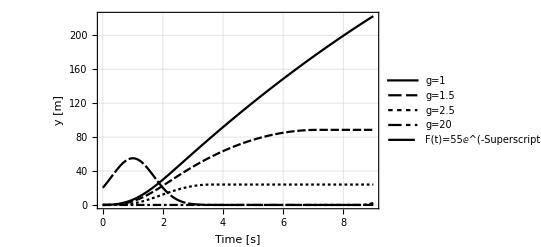

```mathematica
F[t_]=55 ⅇ^(-(t-1)^2);
gF=Plot[Evaluate[{y[t]/.soln[10,10,1.4,1.0,#,2.5,0,0]&/@{1.5,5,9.8,20},F[t]}],
{t,0,9},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"g=1","g=1.5","g=2.5","g=20","F(t)=55ⅇ^(-SuperscriptBox[(t - 1), 2]) [N]"},
GridLines->Automatic,
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'g' With Time Dependant F(t)"}}]
```

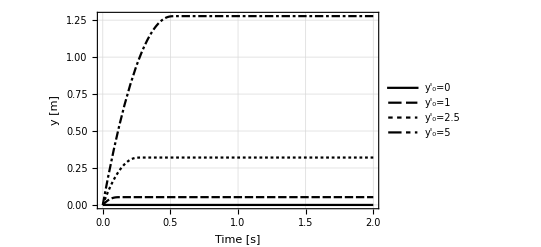

```mathematica
F[t_]=0;
v0=Plot[Evaluate[y[t]/.soln[10,10,1.4,1.0,9.8,5,#,0]&/@{0,1,2.5,5}],
{t,0,2},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"y'_0=0","y'_0=1","y'_0=2.5","y'_0=5"},
GridLines->Automatic,
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'y'_0'"}}]
```

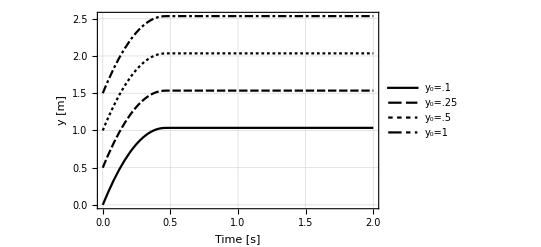

```mathematica
F[t_]=0;
p0=Plot[Evaluate[y[t]/.soln[10,10,1.4,1.0,9.8,5,4.5,#]&/@{0,.5,1,1.5}],
{t,0,2},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"y_0=.1","y_0=.25","y_0=.5","y_0=1"},
GridLines->Automatic,
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'y_0'"}}]
```

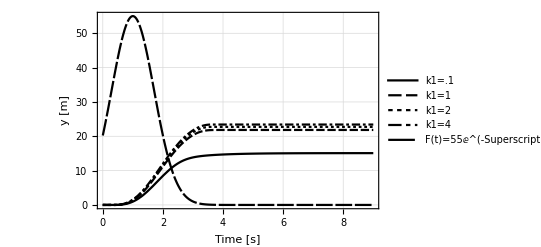

```mathematica
F[t_]=55 ⅇ^(-(t-1)^2);
k1F=Plot[Evaluate[{y[t]/.soln[#,10,1.4,1.0,9.8,2.5,0,0]&/@{.1,1,2,4},F[t]}],
{t,0,9},
PlotRange->All,
PlotTheme->"Monochrome",
PlotLegends->{"k1=.1","k1=1","k1=2","k1=4","F(t)=55ⅇ^(-SuperscriptBox[(t - 1), 2]) [N]"},
GridLines->Automatic,
Frame->True,
FrameLabel->{{"y [m]",None},{"Time [s]","'y' Varying 'k1' With Time Dependant F(t)"}}]
```

```mathematica
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/k1.png",k1];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/k1F.png",k1F];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/k21.png",k21];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/k22.png",k22];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/mF.png",mF];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/p0.png",p0];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/v0.png",v0];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/ks.png",ks];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/ksF.png",ksF];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/kk.png",kk];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/kkF.png",kkF];
Export["~/Wolfram Mathematica/MTU/Diff Equ/Project Images/gF.png",gF];
```